```mathematica
B=1.;
t=1
J=0.4*t;
H=J*{
{0,1/2,1/2,1/2,1/2,0},
{1/2,(2-B),0,0,0,1/2},
{1/2,0,(2-B),0,0,1/2},
{1/2,0,0,(2-B),0,1/2},
{1/2,0,0,0,(2-B),1/2},
{0,1/2,1/2,1/2,1/2,(4-4B)}
};
H//MatrixForm
```

1

(0 | 1/2 | 1/2 | 1/2 | 1/2 | 0
1/2 | 1. | 0 | 0 | 0 | 1/2
1/2 | 0 | 1. | 0 | 0 | 1/2
1/2 | 0 | 0 | 1. | 0 | 1/2
1/2 | 0 | 0 | 0 | 1. | 1/2
0 | 1/2 | 1/2 | 1/2 | 1/2 | 0.)

```mathematica
{e,v}=Eigensystem[H];
p=Ordering[e];
e=e[[p]];
v=v[[p]];
Print["Energy: ",Round[e,10^-15]*1.0//TableForm,"   ","State: ",Grid[Round[v,10^-15]*1.0,Dividers->{False,All}]];
```

Energy: -1.
2.×10^-15
1.
1.
1.
2.   State: 0.57735 | -0.288675 | -0.288675 | -0.288675 | -0.288675 | 0.57735
-0.707107 | 0. | 0. | 0. | 0. | 0.707107
0. | -0.471405 | -0.471405 | 0.235702 | 0.707107 | 0.
0. | 0.0672945 | 0.262837 | -0.825329 | 0.495197 | 0.
0. | -0.72336 | 0.67727 | 0.115225 | -0.0691347 | 0.
-0.408248 | -0.408248 | -0.408248 | -0.408248 | -0.408248 | -0.408248

```mathematica
G[w_]:=1/(w-J-2t^2/(w-3J/2))
```

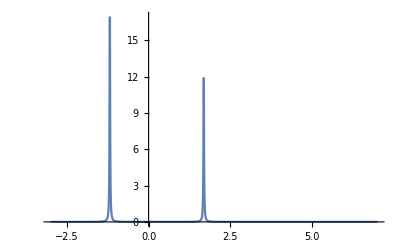

```mathematica
Plot[-Im[G[x+J+0.01I]]/Pi,{x,-3,7},PlotRange->All]
```

```mathematica
0.953674948299421^2
```

0.909496

```mathematica
4*0.149342886705607^2
```

0.0892132